```mathematica
WolframAlpha["Stephen Wolfram curve","PodIDs"]
```

{Input,PlotPod:PopularCurveData,AssociatedEntitiesPod:PopularCurveData,EquationsPod:PopularCurveData,PropertiesPod:PopularCurveData}

```mathematica
curve=WolframAlpha["Elephant Curve",{{"EquationsPod:PopularCurveData",1},"ComputableData"}]
```

{Hold[x[t]==-27/5 Sin[3/2-30 t]-16/3 Sin[9/8-29 t]-29/5 Sin[5/4-27 t]-8/3 Sin[1/4-26 t]-25/7 Sin[1/3-25 t]-31/4 Sin[4/7-22 t]-25/4 Sin[4/3-20 t]-33/2 Sin[2/3-19 t]-67/4 Sin[6/5-16 t]-100/11 Sin[1/4-10 t]-425/7 Sin[1-4 t]+149/4 Sin[8 t]+1172/3 Sin[21/5+t]+661/11 Sin[3+2 t]+471/8 Sin[10/7+3 t]+211/7 Sin[13/4+5 t]+39/4 Sin[10/7+6 t]+139/10 Sin[7/6+7 t]+77/3 Sin[18/7+9 t]+135/8 Sin[1/2+11 t]+23/4 Sin[8/5+12 t]+95/4 Sin[4+13 t]+31/4 Sin[3/5+14 t]+67/11 Sin[7/3+15 t]+127/21 Sin[17/4+17 t]+95/8 Sin[7/8+18 t]+32/11 Sin[8/3+21 t]+81/10 Sin[45/11+23 t]+13/3 Sin[13/4+24 t]+7/4 Sin[3/2+28 t]+11/5 Sin[5/2+31 t]+1/3 Sin[12/5+32 t]+13/4 Sin[22/5+33 t]+14/3 Sin[9/4+34 t]+9/5 Sin[8/5+35 t]+17/9 Sin[22/5+36 t]+1/3 Sin[15/7+37 t]+3/2 Sin[39/10+38 t]+4/3 Sin[7/2+39 t]+5/3 Sin[17/6+40 t]],Hold[y[t]==-13/7 Sin[1/2-40 t]-31/8 Sin[1/11-34 t]-12/5 Sin[1/4-31 t]-9/4 Sin[4/3-29 t]-5/3 Sin[4/3-28 t]-11/2 Sin[6/5-26 t]-17/7 Sin[3/2-25 t]-5/2 Sin[1-24 t]-39/7 Sin[1-19 t]-59/5 Sin[2/3-18 t]-179/9 Sin[13/12-12 t]-103/2 Sin[1/10-9 t]-356/5 Sin[1-5 t]-429/2 Sin[20/19-t]+288/5 Sin[10/3+2 t]+53/6 Sin[5/2+3 t]+351/7 Sin[5/2+4 t]+201/4 Sin[17/7+6 t]+167/3 Sin[19/5+7 t]+323/5 Sin[1/4+8 t]+153/7 Sin[2/3+10 t]+71/5 Sin[6/5+11 t]+47/12 Sin[11/5+13 t]+391/26 Sin[2+14 t]+164/11 Sin[1/7+15 t]+11/2 Sin[2/3+16 t]+31/3 Sin[1/7+17 t]+54/11 Sin[1/4+20 t]+43/5 Sin[13/3+21 t]+13/5 Sin[3/2+22 t]+17/5 Sin[11/5+23 t]+19/10 Sin[4+27 t]+15/2 Sin[55/18+30 t]+4/3 Sin[3/5+32 t]+5/3 Sin[4+33 t]+27/7 Sin[13/6+35 t]+1/4 Sin[43/11+36 t]+16/5 Sin[9/2+37 t]+20/19 Sin[23/6+38 t]+8/3 Sin[4/7+39 t]]}

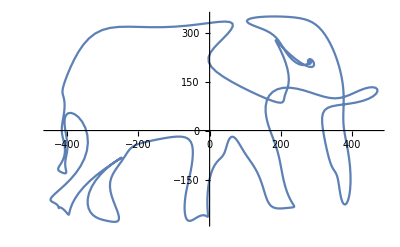

```mathematica
{curveX,curveY}=Last/@(curve//ReleaseHold);
points=Table[{curveX,curveY}/.{t->tt},{t,0,2π,2.π/2^9}];
ListLinePlot[points]
```

```mathematica
With[{
pts=points/Max@Abs@Flatten@points
},
pts//Export[NotebookDirectory[]<>"/elephant.9.json",#,"RawJSON"]&
]
```

C:\Users\Johannes\Programmieren\Q\qhomer\Resources\/elephant.9.json